```mathematica
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

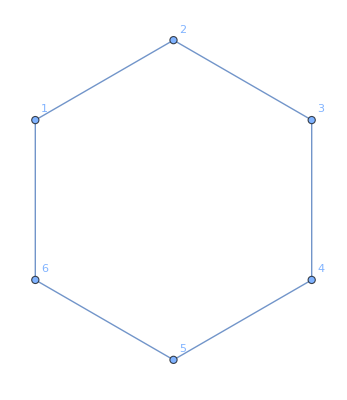

{{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}}

{{0,0,0},{0,0,0},{0,0,0}}

(1 | 0 | 1
1 | 1 | 0
0 | 1 | 1)

(1 | 1 | 0
0 | 1 | 1
1 | 0 | 1)

{-2,2,-1,-1,1,1}

{{2/L,1/L,1/L},{1/L,2/L,1/L},{1/L,1/L,2/L}}

(4-9 L^2+6 L^4-L^6)/L^3

{{L→-2},{L→-1},{L→-1},{L→1},{L→1},{L→2}}

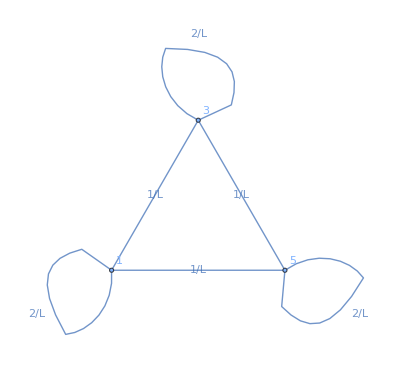

{{1/λ,1/λ,2/λ},{2/λ,1/λ,1/λ},{1/λ,2/λ,1/λ}}

{{2,1,1},{1,2,1},{1,1,2}}

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,5<->6,6<->1}, VertexLabels->"Name"]
A=MyAdjacencyMatrix[G]
S = {1,3,5};
Sbar={2,4,6};
A[[S,S]]
A[[S,Sbar]]//MatrixForm
A[[Sbar,S]]//MatrixForm
Eigenvalues[MyAdjacencyMatrix[G]]
adjmat = Simplify[Smash[G,{1,3,5}]]
Det[adjmat - L IdentityMatrix[3]]
Solve[Det[adjmat - L IdentityMatrix[3]]==0,{L}]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->3,3->5}]
{{1,0,1},{1,1,0},{0,1,1}}.{{1/λ,0,0},{0,1/λ,0},{0,0,1/λ}}.{{1,0,1},{1,1,0},{0,1,1}}
{{1,0,1},{1,1,0},{0,1,1}}.Transpose[{{1,0,1},{1,1,0},{0,1,1}}]
```

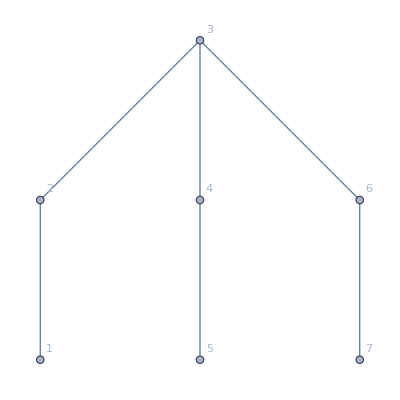

{{0,1,0,0,0,0,0},{1,0,1,0,0,0,0},{0,1,0,1,0,1,0},{0,0,1,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,1},{0,0,0,0,0,1,0}}

{-2,2,-1,-1,1,1,0}

{{2/L,1/L,1/L},{1/L,2/L,1/L},{1/L,1/L,2/L}}

4/L^3-9/L+6 L-L^3

{{L→-2},{L→-1},{L→-1},{L→1},{L→1},{L→2}}

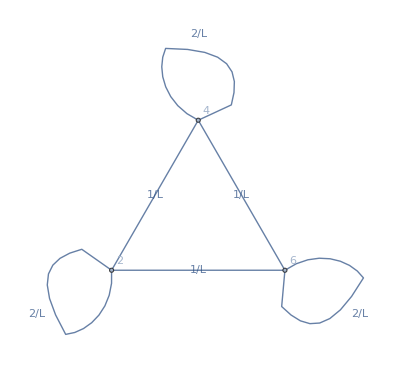

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,3<->6,6<->7}, VertexLabels->"Name"]
MyAdjacencyMatrix[G]
Eigenvalues[MyAdjacencyMatrix[G]]
adjmat = Simplify[Smash[G,{2,4,6}]]
Det[adjmat - L IdentityMatrix[3]]
Solve[Det[adjmat - L IdentityMatrix[3]]==0,{L}]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->2,2->4,3->6}]
```

{{b_1,b_2,b_4},{b_2,b_3,b_5},{b_4,b_5,b_6}}

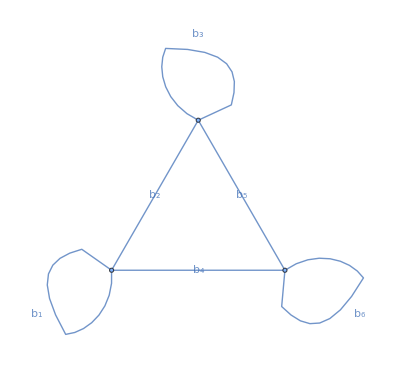

```mathematica
adjmat = {{Subscript[b, 1],Subscript[b, 2],Subscript[b, 4]},{Subscript[b, 2],Subscript[b, 3],Subscript[b, 5]},{Subscript[b, 4],Subscript[b, 5],Subscript[b, 6]}}
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight"]
```

{{a_1,a_2},{a_2,a_3}}

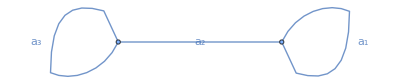

```mathematica
adjmat = {{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 2],Subscript[a, 3]}}
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight"]
```